```mathematica
Quit[]
```

```mathematica
<<"HelicityVariables`"
<<"GraphGenerator`"
<<"YoungSymm`"
```

```mathematica
Options[PlanarMomentumConservation]={"Echos"->False};

PlanarMomentumConservation[{angles_,squares_},momenta_List,OptionsPattern[]]:=
Module[{nonzeroangles=angles["NonzeroPositions"],nonzerosquares=squares["NonzeroPositions"],forbidden={},n=Length[momenta]},

If[momenta[[-2]]!=0,
AppendTo[forbidden,MemberQ[nonzeroangles,{n-1,n}]||MemberQ[nonzerosquares,{n-1,n}]]
];

If[
momenta[[1]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n}],
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{1,n-1}](*,
MemberQ[nonzeroangles,{n-1,n}]&&MemberQ[nonzerosquares,{1,n}],
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{n-1,n}]*)(*,
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{1,n}]*)
}
];
If[
momenta[[-2]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n-1}]
}
]
]
];

If[If[OptionValue["Echos"],Echo[Or@@Echo[forbidden,"Conditions:"]],Or@@forbidden],Return[Nothing],Return[{angles,squares}]]
]
```

```mathematica
Planarise[matrix_,forbiddenEdges_]:=
Module[{x=matrix},
While[
IsGraphNonIntesercting[x]==Nothing,
Print["OPS! If you are not Stefano, please ignore!"];
x=(If[IntersectingQ[#["NonzeroPositions"],forbiddenEdges],Nothing,#]&/@SchoutenCrossing[x]);
x=Part[x,1]
];
Return[x]
]
```

```mathematica
DrawStructure[{adjacencyAngle_,adjacencySquare_},labels_List]:=Show[{DrawAdjacencyGraph[adjacencyAngle,"Colour"->Red],DrawAdjacencyGraph[adjacencySquare,"Colour"->Blue,"Labels"->labels]}]
```

```mathematica
FreeSpinorsAndMomenta[{adjAngle_,adjSquare_},momenta_List,labels_List,spins_List]:=
Module[{newlabels,types,positions,nonmomenta,newangles,newsquares,n,forbiddenEdges},

newlabels=If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}];
positions=FoldPairList[TakeDrop,Range@Length[Flatten@newlabels],Length/@newlabels];
forbiddenEdges=Flatten[Map[Subsets[#,{2}]&,If[Length[#]<2,Nothing,#]&/@positions,{1}],1];

nonmomenta =Part[#,1]&/@positions;

n=Length[Flatten@newlabels];

newangles=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjAngle],{n,n}];
newsquares=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjSquare],{n,n}];

Do[
n=i[[-1]];
Do[
{newangles[[Sequence@@#]]--,newangles[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newangles["NonzeroPositions"],1];
{newsquares[[Sequence@@#]]--,newsquares[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newsquares["NonzeroPositions"],1],
{j,Delete[i,-1]}
],
{i,Reverse/@positions}
];

{newangles,newsquares}=Planarise[#,forbiddenEdges]&/@{newangles,newsquares};

newlabels=Flatten@newlabels;

DrawStructure[{newangles,newsquares},newlabels]

]
```

```mathematica
Options[FromMatrixToSpinors]={"MomentumConservation"->True,"Echos"->True};

FromMatrixToSpinors[{adjAngle_,adjSquare_},momenta_List,labels_List,spins_List,OptionsPattern[]]:=
If[MemberQ[spins,2],
Module[{newlabels,types,positions,nonmomenta,newangles,newsquares,n,forbiddenEdges},

(*Echo[{{adjAngle,adjSquare},momenta}];*)

newlabels=If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}];
positions=FoldPairList[TakeDrop,Range@Length[Flatten@newlabels],Length/@newlabels];
forbiddenEdges=Flatten[Map[Subsets[#,{2}]&,If[Length[#]<2,Nothing,#]&/@positions,{1}],1];

nonmomenta =(* Table[1+Sum[Length[newlabels[[i]]],{i,1,j-1}],{j,1,Length@momenta}]*)Part[#,1]&/@positions;

(*newlabels=Flatten[newlabels];*)
n=Length[Flatten@newlabels];

newangles=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjAngle],{n,n}];
newsquares=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjSquare],{n,n}];

(*newlabels=Flatten[newlabels];*)
(*Echo[{newangles,newsquares}];*)

Do[
n=i[[-1]];
Do[
{newangles[[Sequence@@#]]--,newangles[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@(*Part[Sort[Select[newangles["NonzeroPositions"],MatchQ[#,{n,_}|{_,n}]&]],1]*)
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newangles["NonzeroPositions"],1];
{newsquares[[Sequence@@#]]--,newsquares[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@(*Part[Sort[Select[newsquares["NonzeroPositions"],MatchQ[#,{n,_}|{_,n}]&]],1]*)
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newsquares["NonzeroPositions"],1],
{j,Delete[i,-1]}
],
{i,Reverse/@positions}
];

{newangles,newsquares}=Planarise[#,forbiddenEdges]&/@{newangles,newsquares};

types=Flatten@Table[If[spins[[i]]==1,1,{2,ConstantArray[3,momenta[[i]]]}],{i,Length@positions}];
newlabels=Flatten@newlabels;

(*If[OptionValue["Echos"],Echo[DrawStructure[{newangles,newsquares},newlabels],"New graph:"]];*)

(*If[
TrueQ@OptionValue["MomentumConservation"],
If[PlanarMomentumConservation[{newangles,newsquares},positions,spins],Return[Nothing]]
];*)

Return[(*{newangles,newsquares}*)
Times@@((AngleB[
If[types[[#[[1,1]]]]==1,SpinorML[newlabels[[#[[1,1]]]]],If[types[[#[[1,1]]]]==2,SpinorMV[][newlabels[[#[[1,1]]]]],SpinorMV[$up][newlabels[[#[[1,1]]]],StringJoin["I",ToString[newlabels[[#[[1,1]]]]],ToString[#[[1,1]]]]]]],
If[types[[#[[1,2]]]]==1,SpinorML[newlabels[[#[[1,2]]]]],If[types[[#[[1,2]]]]==2,SpinorMV[][newlabels[[#[[1,2]]]]],SpinorMV[$up][newlabels[[#[[1,2]]]],StringJoin["I",ToString[newlabels[[#[[1,2]]]]],ToString[#[[1,2]]]]]]]]^#[[2]]
)&/@Delete[ArrayRules[newangles],-1])*
Times@@((SquareB[
If[types[[#[[1,1]]]]==1,SpinorML[newlabels[[#[[1,1]]]]],If[types[[#[[1,1]]]]==2,SpinorMV[][newlabels[[#[[1,1]]]]],SpinorMV[$down][newlabels[[#[[1,1]]]],StringJoin["I",ToString[newlabels[[#[[1,1]]]]],ToString[#[[1,1]]]]]]],
If[types[[#[[1,2]]]]==1,SpinorML[newlabels[[#[[1,2]]]]],If[types[[#[[1,2]]]]==2,SpinorMV[][newlabels[[#[[1,2]]]]],SpinorMV[$down][newlabels[[#[[1,2]]]],StringJoin["I",ToString[newlabels[[#[[1,2]]]]],ToString[#[[1,2]]]]]]]]^#[[2]]
)&/@Delete[ArrayRules[newsquares],-1])
]

]
,

If[
TrueQ@OptionValue["MomentumConservation"],
If[PlanarMomentumConservation[{adjAngle,adjSquare},FoldPairList[TakeDrop,Range@Length[Flatten@#],Length/@#],spins]&@(If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}]),Return[Nothing]]
];

Times@@(AngleB[SpinorML[labels[[#[[1,1]]]]],SpinorML[labels[[#[[1,2]]]]]]^#[[2]]&/@Transpose[{adjAngle["NonzeroPositions"],adjAngle["NonzeroValues"]}])*Times@@(SquareB[SpinorML[labels[[#[[1,1]]]]],SpinorML[labels[[#[[1,2]]]]]]^#[[2]]&/@Transpose[{adjSquare["NonzeroPositions"],adjSquare["NonzeroValues"]}])
]
```

```mathematica
Options[SpinStructures]={"MomentumConservation"->True,"Echos"->False};

SpinStructures[{{anglestructure_List,squarestructure_List},momenta_List},labels_List,spins_List,OptionsPattern[]]:=
Module[{formfactors,angles,squares},

angles=AllNonIntersectingGraphs[anglestructure];
squares=AllNonIntersectingGraphs[squarestructure];

formfactors=Tuples[{angles,squares}];

If[OptionValue["Echos"],
Echo[momenta,"Momenta:"];
Echo[Map[DrawStructure[#,labels]&,formfactors,{1}],"Graphs before momentum conservation:"];
If[MemberQ[spins,2],Echo[FreeSpinorsAndMomenta[#,momenta,labels,spins]&/@formfactors,"Graphs with momenta:"]];
];

If[
OptionValue["MomentumConservation"],
formfactors=PlanarMomentumConservation[#,momenta,"Echos"->OptionValue["Echos"]]&/@formfactors;
];

If[OptionValue["Echos"],
If[¬MatchQ[formfactors,{}],Echo[Map[DrawStructure[#,labels]&,formfactors,{1}],"Graphs:"],Echo["No graph survided."]]
];

formfactors=FromMatrixToSpinors[#,momenta,labels,spins,"MomentumConservation"->OptionValue["MomentumConservation"],"Echos"->OptionValue["Echos"]]&/@formfactors;

Return[formfactors];
]
```

```mathematica
Options[UniformMassStructres]={"MomentumConservation"->True,"Echos"->False};

UniformMassStructres[dim_Integer,OptionsPattern[]][list__]:=
Module[{labels=Part[#,1]&/@{list},spins=Delete[#,1]&/@{list},angles,squares,structures},

{angles,squares}=
Transpose[
If[Length[#]==1,
{Abs[#[[1]]]-#[[1]],Abs[#[[1]]]+#[[1]]},
{#[[1]]-#[[2]],#[[1]]+#[[2]]}
]&/@spins
];

If[
TrueQ@OptionValue["MomentumConservation"],
structures=(Append[#,0]&/@PermutationsOfPartitions[dim-Total[angles]/2-Total[squares]/2,Length[angles]-1]),
structures=PermutationsOfPartitions[dim-Total[angles]/2-Total[squares]/2,Length[angles]]
];

structures={{angles+#,squares+#},#}&/@structures;

structures=If[Length[#[[1]]]<2,Nothing,#]&/@(MapAt[Map[IsLoopLessDoable,#,{1}]&,#,1]&/@structures);

structures=SpinStructures[#,labels,Length/@spins,"MomentumConservation"->OptionValue["MomentumConservation"],"Echos"->OptionValue["Echos"]]&/@structures;

structures=Flatten[structures,1];

Return[(*Flatten@*)structures]

]
```

```mathematica
Options[IndependentSpinStructres]={"MomentumConservation"->True,"MassSquared"->False};

IndependentSpinStructres[dim_Integer,OptionsPattern[]][list__?((Length[#]==2 && IntegerQ[2*#[[2]]])||(Length[#]==3 && IntegerQ[2*#[[2]]] && IntegerQ[2*#[[3]]] && #[[2]]>=Abs[#[[3]]])&)]:=
Module[{massivespins=Table[If[Length[i]==2,0,i[[2]]],{i,{list}}],x= Table[If[Length[i]==2,0,i[[3]]],{i,{list}}],momenta=dim-Sum[i[[2]],{i,{list}}],n=Length[{list}]},

If[momenta<0,{}];

massivespins=Tuples[(Range[-#,#,1])&/@massivespins];
massivespins={Abs[#-x],#}&/@massivespins;
massivespins={Product[Mass[{list}[[i,1]]]^#[[1,i]],{i,n}],Total@#[[1]],Table[If[Length[{list}[[i]]]==2,{list}[[i]],{{list}[[i,1]],{list}[[i,2]],#[[2,i]]}],{i,n}]}&/@massivespins;

massivespins=SortBy[massivespins,#[[1]]&];

massivespins=#[[1]]*UniformMassStructres[dim-#[[2]],"MomentumConservation"->OptionValue["MomentumConservation"]][Sequence@@#[[3]]]&/@massivespins;

If[momenta-2>=0&&OptionValue["MassSquared"],
x=Table[If[Length[i]==2,Nothing,Mass[i[[1]]]^2],{i,{list}}];
massivespins=
Join[
massivespins,
Times@@@Tuples[{x,Flatten@IndependentSpinStructres[dim-2,"MomentumConservation"->OptionValue["MomentumConservation"],"MassSquared"->OptionValue["MassSquared"]][list]}]
];
];

Return[Flatten@massivespins]

]
```

Momenta:  {3,3,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-}

Momenta:  {3,0,3,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {True,False,False,True}

True

No graph survided.

Momenta:  {0,3,3,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

Momenta:  {3,2,1,0}

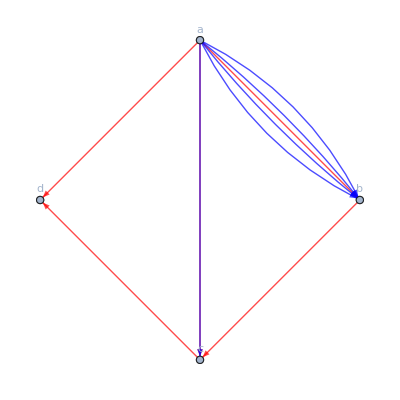
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,True}

True

Conditions:  {False,False,True,True}

True

Conditions:  {True,False,True,True}

True

No graph survided.

Momenta:  {3,1,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Conditions:  {True,False,False,True}

True

Conditions:  {True,False,True,True}

True

No graph survided.

Momenta:  {2,3,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False,False,False}

False

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

Graphs:  {-Graphics-}

Momenta:  {2,1,3,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {True,False,False,True}

True

No graph survided.

Momenta:  {1,3,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

No graph survided.

Momenta:  {1,2,3,0}

Graphs before momentum conservation:  {-Graphics-}

Conditions:  {True,False,False,True}

True

No graph survided.

Momenta:  {2,2,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Conditions:  {True,False,False,True}

True

Conditions:  {True,False,True,True}

True

No graph survided.

{ab^3 cd^2 ab^5,ab ad^2 bc^2 ab^5,ab^2 ad bc cd ab^5,ad^2 bc^3 ab^4 bc}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True,"Echos"->True][{a,1},{b,1},{c,-1},{d,-1}]
```

```mathematica
Length/@(UniformMassStructres[21,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,0},{2,1,0},{3,1,0},{4,1}}]))
```

{10,10,10,10,11,11,10,10,10,10,11,11,10,10,10,10,11,11,11,11,11,11,11,11}

Momenta:  {1,3,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

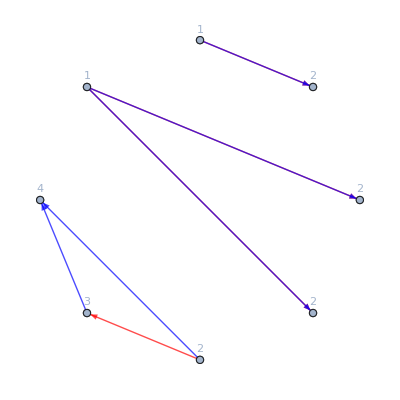
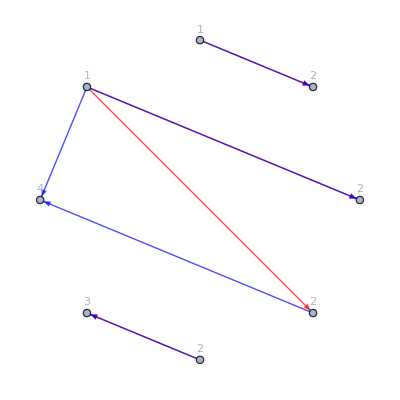
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {1,0,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

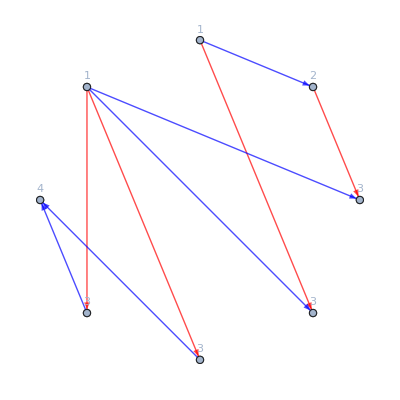
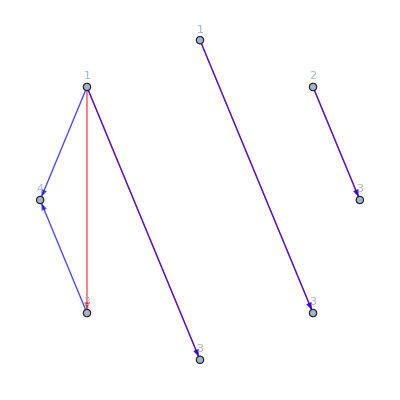
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False,False,True}

True

Conditions:  {True,True,False,True}

True

No graph survided.

Momenta:  {0,3,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

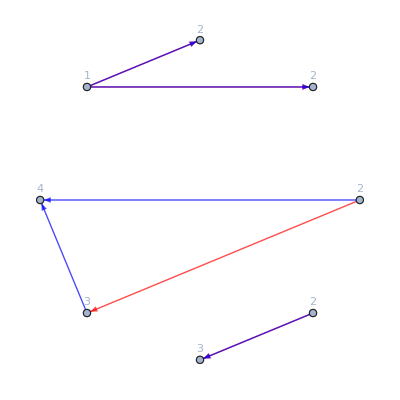
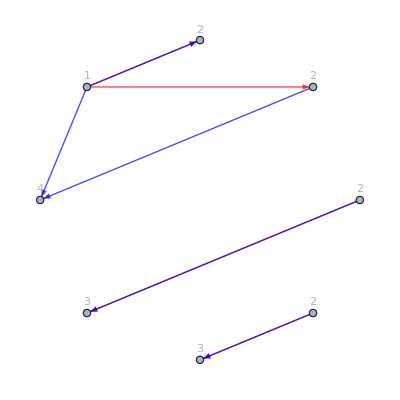
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {False}

False

Graphs:  {-Graphics-}

Momenta:  {0,1,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

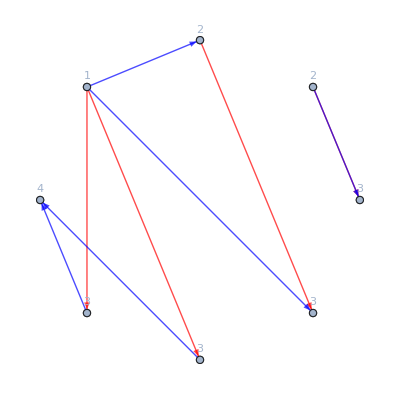
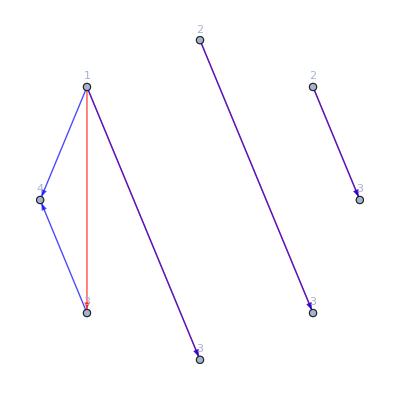
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {2,2,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

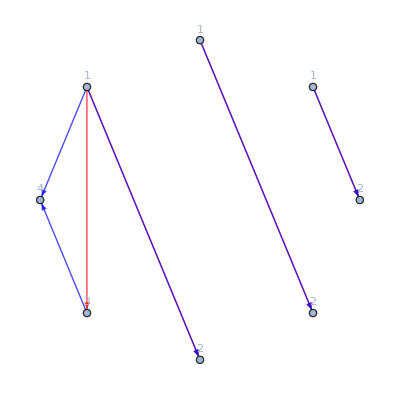
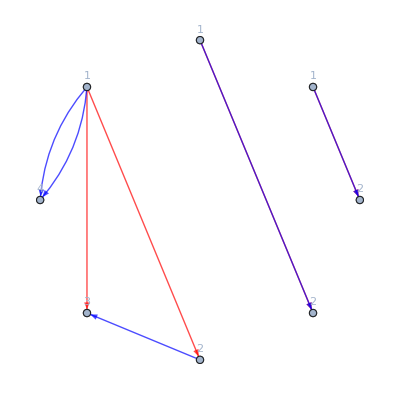
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False}

True

Conditions:  {True,False}

True

No graph survided.

Momenta:  {2,0,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

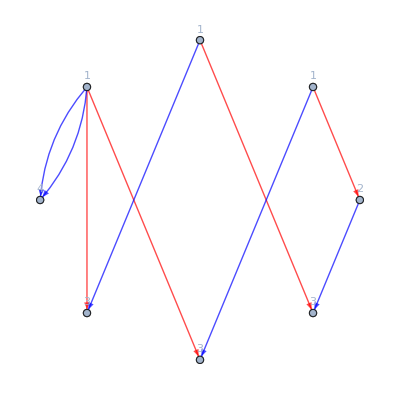
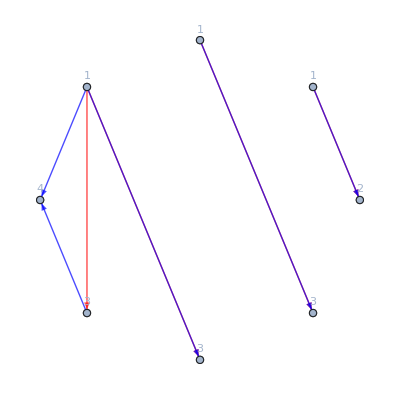
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,True,False,True}

True

Conditions:  {True,True,False,True}

True

No graph survided.

Momenta:  {0,2,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

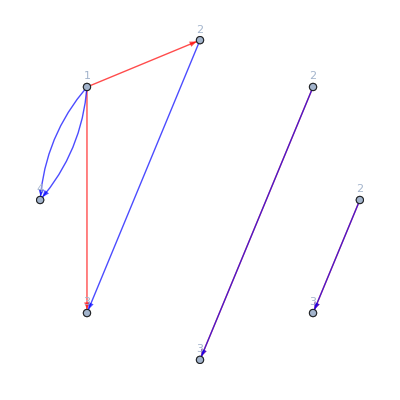
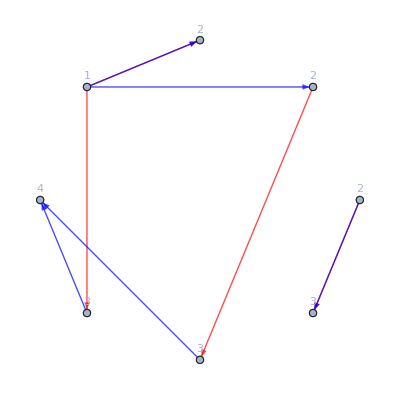
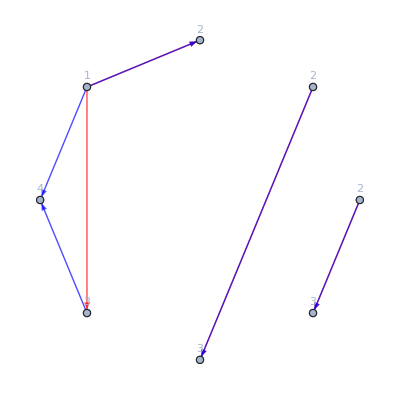
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False}

False

Conditions:  {True}

True

Conditions:  {True}

True

Graphs:  {-Graphics-}

Momenta:  {2,1,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

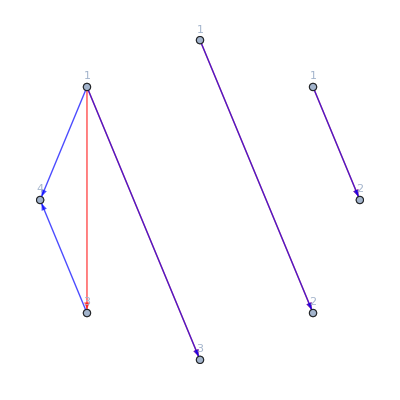
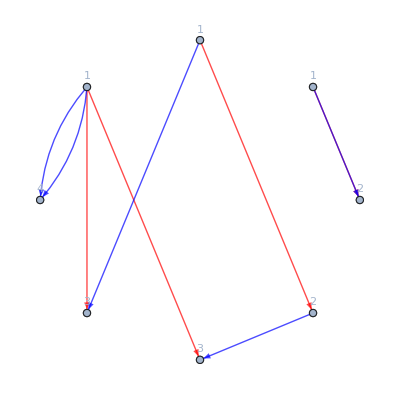
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,True,False,True}

True

Conditions:  {False,True,False,True}

True

No graph survided.

Momenta:  {1,2,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

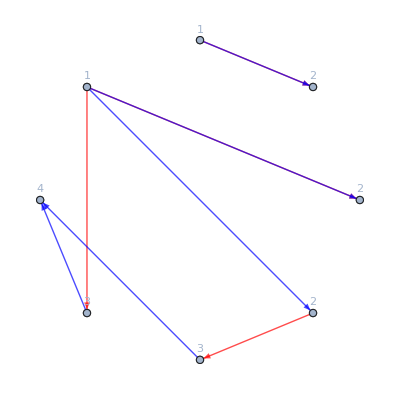
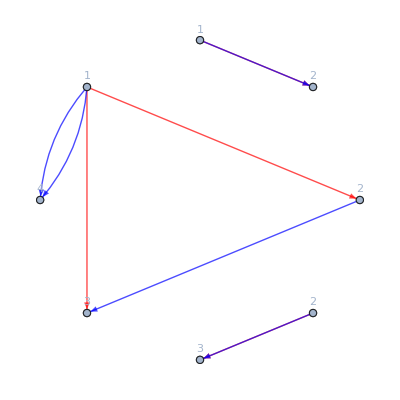
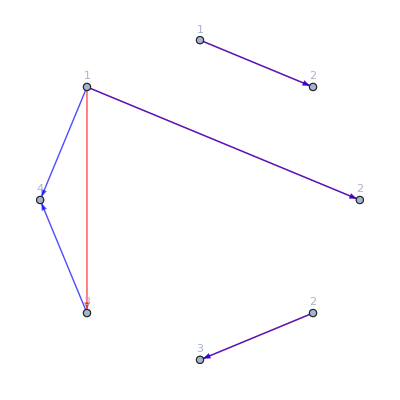
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,False}

True

Conditions:  {False,True,False,False}

True

Conditions:  {True,True,False,False}

True

No graph survided.

Momenta:  {1,1,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

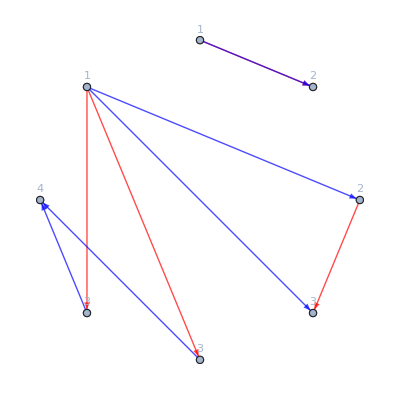
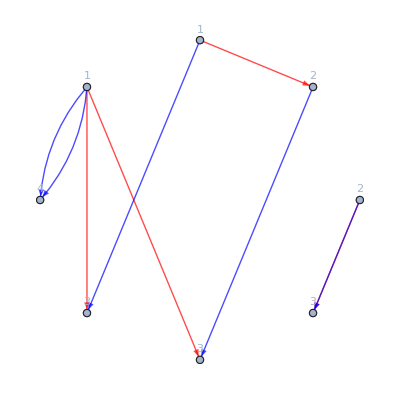
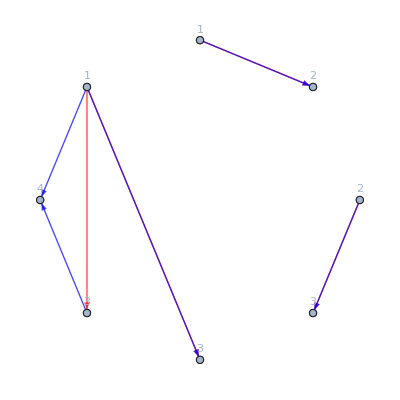
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,True}

True

Conditions:  {False,True,False,True}

True

Conditions:  {True,True,False,True}

True

No graph survided.

{-(11p_2)^2 22p_1 34p_2 43,14p_2 11p_2 22p_1 33p_2 41,-12 14p_2 33p_2 2I242I24p_3 41 12,-12 12p_3 33p_2 2I232I23p_3 41^2}

4

```mathematica
UniformMassStructres[9,"MomentumConservation"->True,"Echos"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
%//Length
```

```mathematica
IndependentSpinStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
```

{-(11p_2)^2 22p_1 34p_2 43,14p_2 11p_2 22p_1 33p_2 41,-12 14p_2 33p_2 2I242I24p_3 41 12,-12 12p_3 33p_2 2I232I23p_3 41^2,-12 (14p_2)^2 33p_2 1 12,-13 14p_2 11p_2 22p_1 1 43,-11p_3p_2 12 33p_2 1 41 42,11p_2 22p_1 31p_2 1 41 43,-11p_2 22p_1 33p_2 1 41^2,12 33p_2 2I232I23p_3 1 41^2 12,-11p_3 22p_3 33p_2 1 41^2,-12 13 14p_2 13p_2 1^2 42,-22p_1 31p_2 1^2 41^2 13,21p_3 33p_2 1^2 41^2 12,12p_2p_1 12 33p_2 2 41^2,-12p_2p_1 12 31p_2 2 41 43,12^2 33p_2 2I232I23p_3 2 41^2,-(14p_2)^2 33p_2 2 12^2,13 14p_2 2 43 12 12p_2p_1,-11p_3p_2 33p_2 2 41 42 12,-(12p_3)^2 33p_2 2 41^2,-12^2 11p_2 34p_2 1 2 43,12^2 14p_2 33p_2 1 2 41,-13 14p_2 13p_2 1 2 42 12,-13 13p_2 12p_3 1 2 41 42,-23p_1p_2 12 1 2 41^2 13,12 21p_3 33p_2 1 2 41^2,-11p_2 34p_2 1 2 43 12^2,14p_2 33p_2 1 2 41 12^2,12p_3 33p_2 1 2 41^2 12,-12^2 13 14p_2 1^2 2 43,-23 21p_3 1^2 2 41^2 13,31p_2 1^2 2 41 43 12^2,-33p_2 1^2 2 41^2 12^2,-12 11p_2 (34p_2)^2 3 12,-13p_3p_2 12 34p_2 3 41 12,13p_3p_2 23 12p_3 3 41^2,-(11p_2)^2 22p_1 3 43^2,-(13p_2)^2 22p_1 3 41^2,11p_2 13p_2 22p_1 3 41 43,-12 13p_2 3 41^2 23p_3p_2,-12 13 14p_2 34p_2 1 3 12,-13p_3p_2 12 13 1 3 41 42,12 (13p_2)^2 1 3 41 42,-12 14p_2 13p_2 1 3 43 12,12 34p_2 31p_2 1 3 41 12,-13p_3p_2 23 1 3 41^2 12,11p_2 22p_1 1 3 41 43 13,-13p_2 22p_1 1 3 41^2 13,-12 1 3 41^2 23 13p_3p_2,-12 13^2 14p_2 1^2 3 42,23 31p_2 1^2 3 41^2 12,-22p_1 1^2 3 41^2 13^2,-21p_3 1^2 3 41^2 13 23,12^2 34p_2 31p_2 2 3 41,-13p_3p_2 12 23 2 3 41^2,-12 13p_2 23p_1 2 3 41^2,-12p_2p_1 12 2 3 41 43 13,-13 14p_2 34p_2 2 3 12^2,-13p_3p_2 13 2 3 41 42 12,-14p_2 13p_2 2 3 43 12^2,(13p_2)^2 2 3 41 42 12,-13p_2 12p_3 2 3 41^2 23,12^2 13 34p_2 1 2 3 41,-12^2 11p_2 1 2 3 43^2,12^2 13p_2 1 2 3 41 43,-13^2 14p_2 1 2 3 42 12,-13^2 12p_3 1 2 3 41 42,12 23 31p_2 1 2 3 41^2,-23^2 11p_3 1 2 3 41^2,-12 23p_1 1 2 3 41^2 13,13 34p_2 1 2 3 41 12^2,-11p_2 1 2 3 43^2 12^2,13p_2 1 2 3 41^2 12 23,13p_2 1 2 3 41 43 12^2,-11p_3 1 2 3 41^2 23^2,1^2 2 3 41 43 12^2 13,1^2 2 3 41^2 12 13 23}

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{4,1},{3,1,0},{1,2,0},{2,1,0}]//Length
```

5

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
UniformMassStructres[7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]
```

{-12 11p_2 34p_2 43 12,12 14p_2 33p_2 41 12,12 12p_3 33p_2 41^2}

{-24 34p_2 41p_2 12 34,24 33p_2 44p_2 12 14,-14 24 33p_2 12 14^2}

```mathematica
IndependentSpinStructres[7,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]//Length
IndependentSpinStructres[7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

30

39

3

Momenta:  {1,0,0,0}

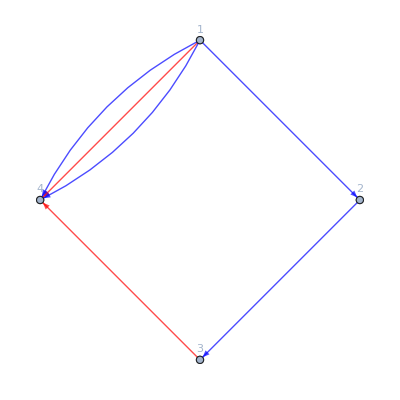
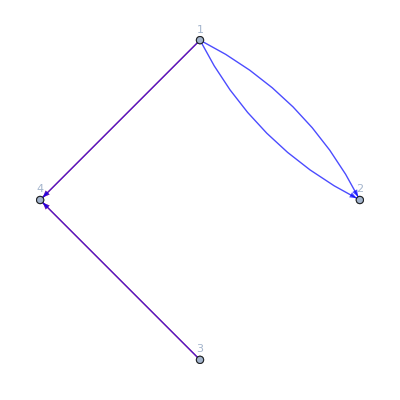
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,1,0,0}

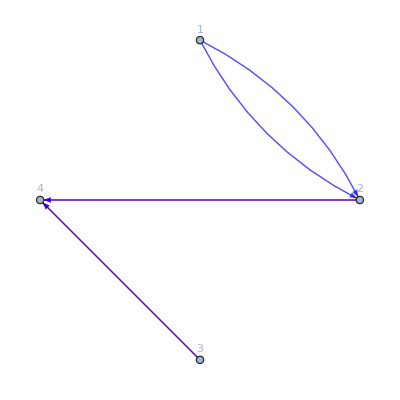
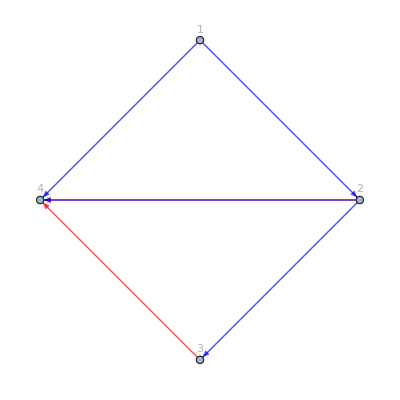
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

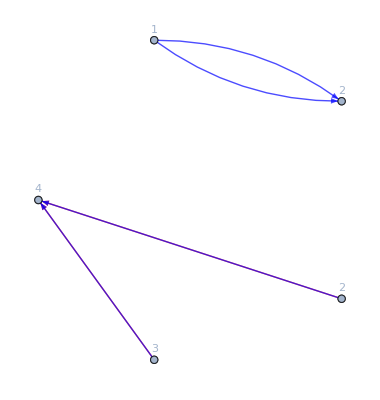
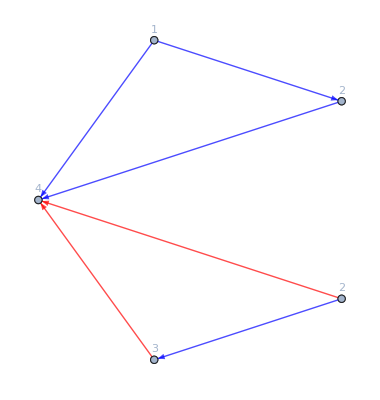
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

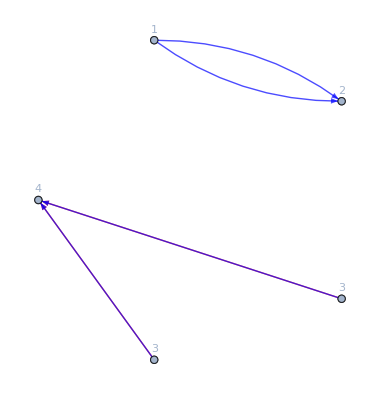
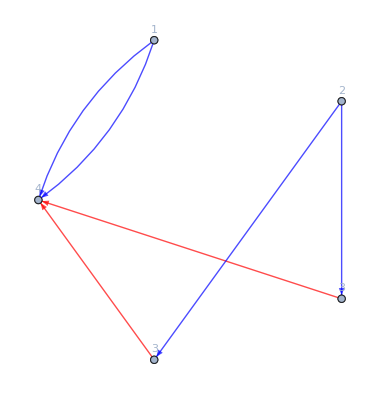
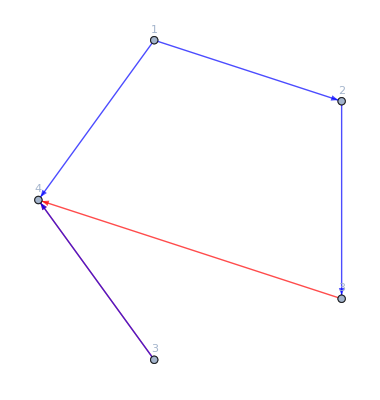
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

4

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,2,0},{2,1,1},{3,1,0},{4,1}]//Length
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,1},{2,1,1},{3,1,0},{4,2,0}]//Length
```

Momenta:  {0,2,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

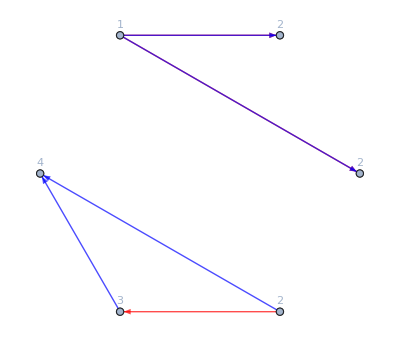
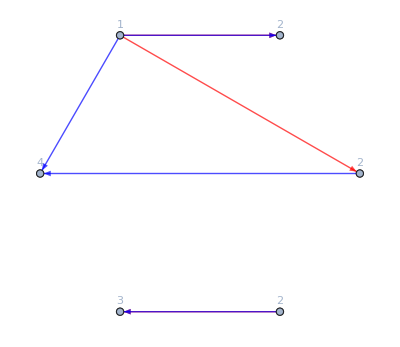
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

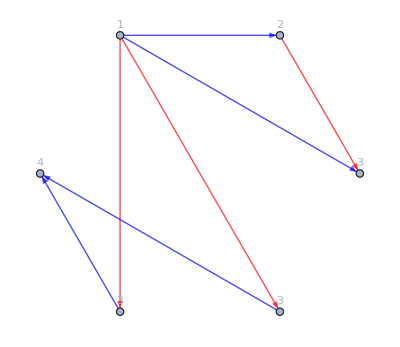
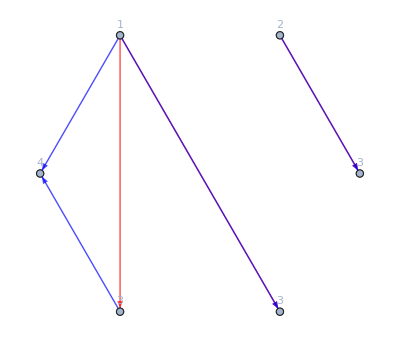
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

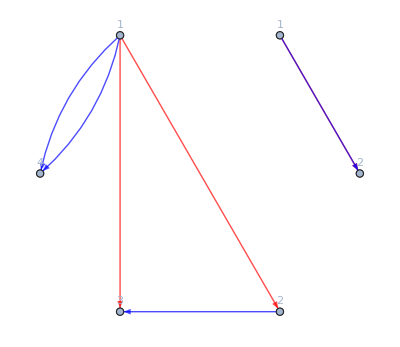
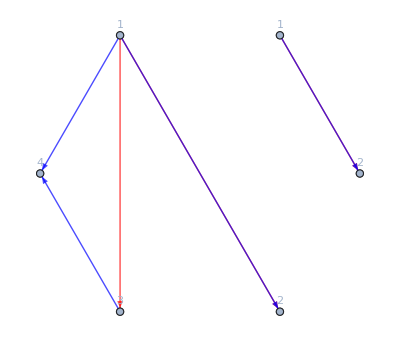
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False}

True

Conditions:  {True,False}

True

No graph survided.

Momenta:  {1,0,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

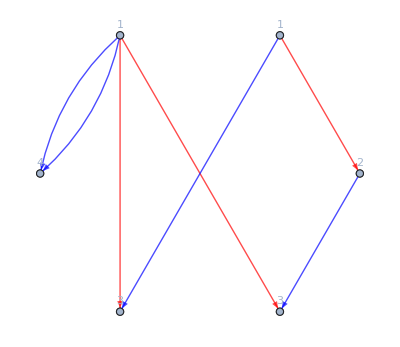
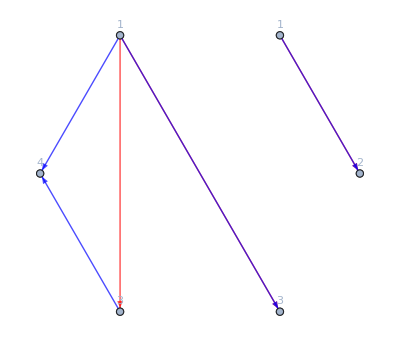
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,True,False,True}

True

Conditions:  {True,True,False,True}

True

No graph survided.

Momenta:  {0,1,1,0}

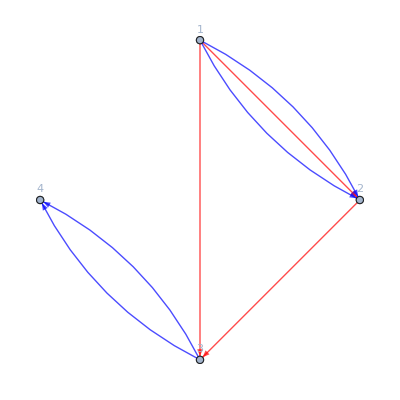
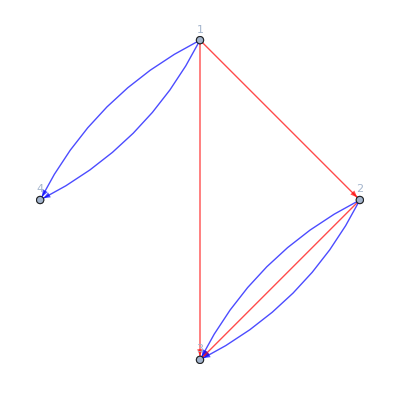
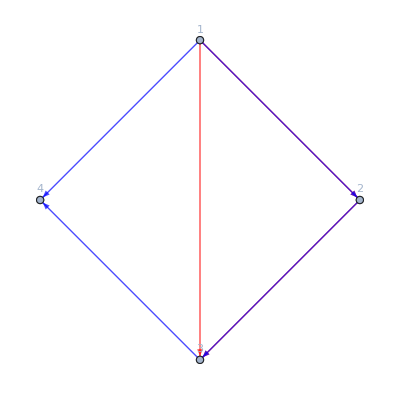
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

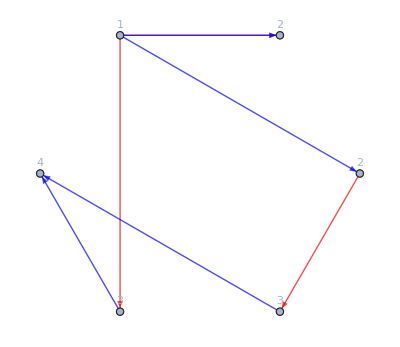
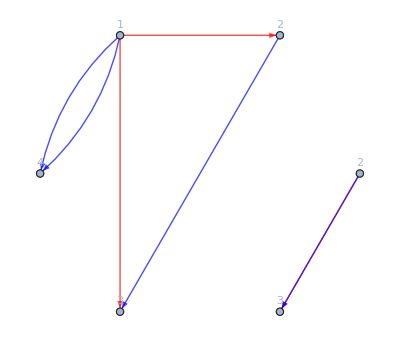
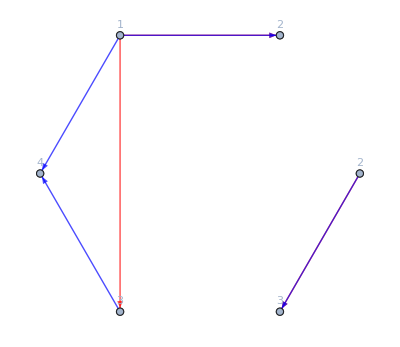
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {False}

False

Conditions:  {True}

True

Graphs:  {-Graphics-}

3

Momenta:  {2,0,0,0}

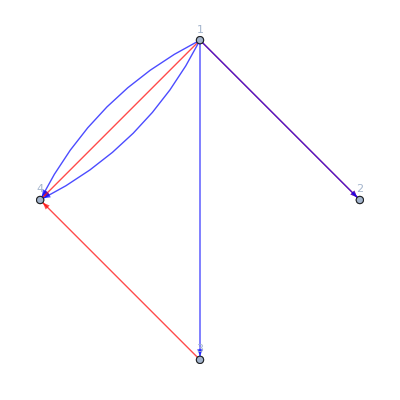
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,True}

True

Conditions:  {False,True}

True

No graph survided.

Momenta:  {0,2,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

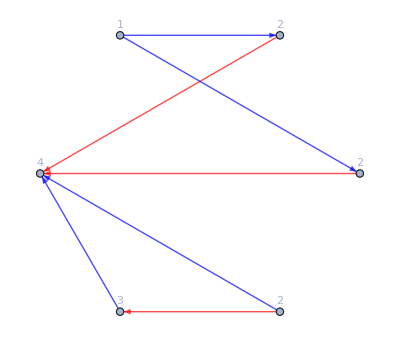
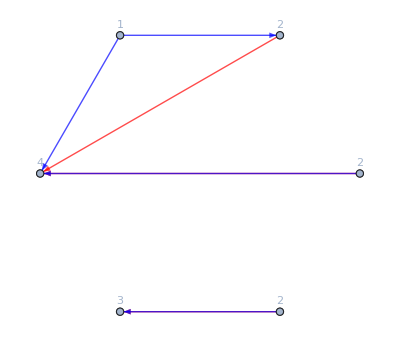
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {1,0,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,True,False}

True

Conditions:  {True,False,True,False}

True

No graph survided.

Momenta:  {0,1,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

6

```mathematica
UniformMassStructres[7,"MomentumConservation"->True,"Echos"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]//Length
UniformMassStructres[7,"MomentumConservation"->True,"Echos"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

```mathematica
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,1},{2,1,1},{3,1,0},{4,2,2}]
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,2,2},{2,1,1},{3,1,0},{4,1}]
```

Momenta:  {1,0,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False}

True

Conditions:  {True,False}

True

No graph survided.

Momenta:  {0,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

{-33p_2 14^2 24^2,-34p_2 12 14 24 34}

Momenta:  {1,0,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True,False}

True

No graph survided.

Momenta:  {0,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

{31p_2 41 43 12^2,-33p_2 41^2 12^2}

```mathematica
Length/@(UniformMassStructres[9,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,0},{2,1,0},{3,1,0},{4,1}}]))
```

{4,4,4,4,5,5,4,4,4,4,5,5,4,4,4,4,5,5,5,5,5,5,5,5}

```mathematica
UniformMassStructres[11,"MomentumConservation"->True][{1,2,0},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[11,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,0}]//Length
```

5

5

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1},{3,1,0},{4,1}]//Length
UniformMassStructres[10,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,1},{3,1},{4,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True,"Echos"->True][{1,1},{2,1},{3,1,0},{4,1,0}]//Length
```

5

Momenta:  {2,4,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False,False}

False

Graphs:  {-Graphics-}

Momenta:  {2,0,4,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True,False,False,True}

True

No graph survided.

Momenta:  {0,4,2,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False}

False

Graphs:  {-Graphics-}

Momenta:  {0,2,4,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

Momenta:  {1,4,1,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False,False,False,False}

False

Graphs:  {-Graphics-}

Momenta:  {1,1,4,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True,False,False,True}

True

No graph survided.

Momenta:  {3,3,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {3,0,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,True,True,True}

True

Conditions:  {True,False,True,True}

True

No graph survided.

Momenta:  {0,3,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False}

False

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Graphs:  {-Graphics-}

Momenta:  {3,2,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False,True,True}

True

Conditions:  {False,True,True,True}

True

No graph survided.

Momenta:  {3,1,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,True,True,True}

True

Conditions:  {True,False,True,True}

True

No graph survided.

Momenta:  {2,3,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

Conditions:  {False,False,False,False}

False

Conditions:  {True,False,False,False}

True

Graphs:  {-Graphics-}

Momenta:  {2,1,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,True,False,True}

True

Conditions:  {True,False,False,True}

True

Conditions:  {False,True,True,True}

True

Conditions:  {True,False,True,True}

True

No graph survided.

Momenta:  {1,3,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False,False,False}

False

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

Graphs:  {-Graphics-}

Momenta:  {1,2,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,True,True,True}

True

Conditions:  {True,False,True,True}

True

Conditions:  {True,True,False,True}

True

Conditions:  {True,False,False,True}

True

No graph survided.

Momenta:  {2,2,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,True,False,True}

True

Conditions:  {True,False,False,True}

True

Conditions:  {False,True,True,True}

True

Conditions:  {True,False,True,True}

True

No graph survided.

8

Momenta:  {4,2,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True,True}

True

No graph survided.

Momenta:  {4,0,2,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False,True,True,True}

True

No graph survided.

Momenta:  {2,4,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False,False}

False

Graphs:  {-Graphics-}

Momenta:  {0,4,2,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False}

False

Graphs:  {-Graphics-}

Momenta:  {4,1,1,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False,True,True,True}

True

No graph survided.

Momenta:  {1,4,1,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False,False,False,False}

False

Graphs:  {-Graphics-}

Momenta:  {3,3,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {3,0,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False,False,True}

True

Conditions:  {True,True,False,True}

True

No graph survided.

Momenta:  {0,3,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {3,2,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,True}

True

Conditions:  {True,True,False,True}

True

Conditions:  {True,False,True,True}

True

Conditions:  {False,True,True,True}

True

No graph survided.

Momenta:  {3,1,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,True}

True

Conditions:  {True,True,False,True}

True

Conditions:  {True,False,True,True}

True

Conditions:  {False,True,True,True}

True

No graph survided.

Momenta:  {2,3,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,False}

True

Conditions:  {False,False,False,False}

False

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

Graphs:  {-Graphics-}

Momenta:  {2,1,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,True,False,True}

True

Conditions:  {True,False,False,True}

True

No graph survided.

Momenta:  {1,3,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False,False,False}

False

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

Conditions:  {True,False,False,False}

True

Graphs:  {-Graphics-}

Momenta:  {1,2,3,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,True,False,True}

True

Conditions:  {True,False,False,True}

True

No graph survided.

Momenta:  {2,2,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,True,True}

True

Conditions:  {False,True,True,True}

True

Conditions:  {True,False,False,True}

True

Conditions:  {True,True,False,True}

True

No graph survided.

9

```mathematica
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==56,#,Nothing]&/@Permutations[{{1,2,0},{2,1},{3,1,0},{4,1},{5,2}}]
```

{}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,1},{3,2},{4,2,0},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,2},{4,1},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,1,0},{4,1},{5,2}]//Length
```

56

47

47

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,2,0},{4,2,0}]
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,1,0},{4,2,0}]
```

{12 (33p_2)^2 (44p_2)^2 12,34 11p_2 22p_1 33p_2 44p_2 34,14 22p_1 (33p_2)^2 44p_2 14,-14 24 (33p_2)^2 2I232I23p_3 14 24,-34^2 11p_2 22p_1 1I121I12p_2 34^2,14 22p_1 (33p_2)^2 44p_1 14,14 22p_3 (33p_2)^2 44p_1 14}

{14 (22p_1)^2 33p_2 44p_1 14,12 22p_1 33p_2 (44p_2)^2 12,-12 24 33p_2 44p_2 2I242I24p_3 12 24,34 11p_2 (22p_1)^2 44p_2 34,14 (22p_1)^2 33p_2 44p_2 14,-14 24 22p_3 33p_2 2I232I23p_3 14 24,14 22p_1 22p_3 33p_2 44p_1 14,-14 24 22p_1 33p_2 2I242I24p_3 14 24,14 (22p_3)^2 33p_2 44p_1 14}

```mathematica
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]//Length
```

Momenta:  {1,0,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True,True,True,True}

True

No graph survided.

Momenta:  {0,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {0,0,1,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

4

```mathematica
UniformMassStructres[8,"MomentumConservation"->True,"Echos"->True][{1,0,0},{2,2,0},{3,1,0},{4,2,0}]//Length
```

Momenta:  {3,0,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False,False,False}

False

Conditions:  {False,False,False,True}

True

Conditions:  {False,False,True,False}

True

Conditions:  {False,False,True,True}

True

Graphs:  {-Graphics-}

Momenta:  {0,0,3,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

Momenta:  {2,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False,False,False}

False

Conditions:  {False,False,True,False}

True

Conditions:  {False,False,False,True}

True

Conditions:  {False,False,False,False}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {2,0,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,False,False,False,False}

True

Conditions:  {True,False,False,True,False,False,False}

True

Conditions:  {True,False,False,True,False,False,False}

True

Conditions:  {True,False,False,False,True,False,False}

True

Conditions:  {False,False,False,False,False,False,True}

True

Conditions:  {True,False,False,False,True,False,True}

True

Conditions:  {True,False,False,False,True,False,False}

True

Conditions:  {True,False,False,True,False,False,True}

True

Conditions:  {True,False,False,True,True,False,True}

True

No graph survided.

Momenta:  {1,2,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False,False,False,False}

False

Graphs:  {-Graphics-}

Momenta:  {1,0,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,False,False,False,False,False,False}

True

Conditions:  {True,False,False,True,False,False,False}

True

Conditions:  {True,False,False,False,True,False,False}

True

Conditions:  {True,False,False,True,True,False,True}

True

No graph survided.

Momenta:  {0,2,1,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {False}

False

Graphs:  {-Graphics-}

Momenta:  {0,1,2,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False,False,False,False,False,True}

True

Conditions:  {True,False,False,False,True,False,False}

True

Conditions:  {True,False,False,True,False,False,False}

True

Conditions:  {True,False,False,False,False,False,False}

True

No graph survided.

5

```mathematica
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==10,#,Nothing]&/@Permutations[{{1,1,0},{2,1,0},{3,2,0},{4,2,0}}]
```

{}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,2,0},{2,1},{3,1,0},{4,1},{5,2}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2},{3,1},{4,2,0},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,1,0},{4,1},{5,2}]//Length
```

47

47

47

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,1,0},{a,1,0},{b,2},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,2,0},{3,1,0},{a,1,0},{b,1,0},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,1,0},{3,1,0},{a,2,0},{b,1,0},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,0},{3,1,0},{a,2,0},{b,1,0},{4,1,0}]//Length
```

240

240

240

«1 more identical outputs»

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1,1},{3,1,0},{4,1,1},{5,1}]//Length
UniformMassStructres[6,"MomentumConservation"->True][{1,1,1},{2,1},{3,1},{4,1,1},{5,1,0}]//Length
```

11

11

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2},{2,1},{3,1},{4,1},{5,1},{6,2},{7,1}]//Length
UniformMassStructres[9,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2},{5,1},{6,1},{7,2}]//Length
```

50

50

```mathematica
Length/@(UniformMassStructres[21,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,1},{2,1,0},{3,1,0},{4,1,0}}]))
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
UniformMassStructres[21,"MomentumConservation"->True][{1,2,1},{2,1,0},{3,1,0},{4,1,0}]//Length
UniformMassStructres[21,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,2,1}]//Length
```

10

10

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,2,0},{2,1},{3,1},{4,1}]
(*UniformMassStructres[6,"MomentumConservation"->True][{4,2,1},{2,1},{3,1},{1,1}]
UniformMassStructres[5,"MomentumConservation"->True][{4,2,2},{2,1},{3,1},{1,1}]
UniformMassStructres[6,"MomentumConservation"->True][{4,2,-1},{2,1},{3,1},{1,1}]//Length
UniformMassStructres[5,"MomentumConservation"->True][{4,2,-2},{2,1},{3,1},{1,1}]//Length*)
```

{21^2 23 24 21^2 34,21^2 23^2 24 21 41,21 31 23^3 41^2}

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,0}]
(*UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,1}]
UniformMassStructres[5,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,2}]
UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,-1}]//Length
UniformMassStructres[5,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,-2}]//Length*)
```

{24^2 12^2 23 24 34,24^2 12 14 23^2 24}

```mathematica
IndependentSpinStructres [7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,0,0}]
```

{-12 11p_2 31p_2 12 13,-21p_3 33p_2 2I232I23p_3 12,12 33p_2 12 11p_2p_3,-(21p_3)^2 33p_2 2,-12 21p_3 31p_2 2 13,-13 11p_2 2 12^2 13,11p_2 33p_2 2 12^2,33p_2 2I232I23p_3 2 12^2,12 (31p_2)^2 3 12,-23p_3p_2 31p_2 3 12,-12 11p_2 3 12 13^2,21p_3 3 23 13p_3p_2,-12 3 12 13 13p_3p_2,-23 21p_3 31p_2 2 3,-12 21p_3 2 3 13^2,13 31p_2 2 3 12^2,13p_2 2 3 12^2 13,-2 3 12 23 13p_3p_2}

```mathematica
(*Permutations@{a,b,c}
YoungSymmetrise[f[Sequence@@#],{{#[[1]],#[[2]]},{#[[3]]}}]&/@%
f[Sequence@@#]&/@%%
Coefficient[#,%]&/@%%
NullSpace[Transpose@%]
(%%.#)&/@%
(#.%%%)&/@%%*)
```

Old momentum conservation, which could be useful at some point.

```mathematica
(*PlanarMomentumConservation[{angles_,squares_},labels_List,spins_List]:=
Module[{nonzeroangles=angles["NonzeroPositions"],nonzerosquares=squares["NonzeroPositions"],forbidden},

forbidden=
Join[
Flatten[
Permutations/@
If[spins[[-2]]==2,
{{_,#[[1]]},{#[[1]],#[[2]]}}&/@Tuples[{Delete[labels[[-2]],-1],labels[[-1]]}],
{{{labels[[-2,1]],labels[[-1,1]]},{_,labels[[-2,1]]}}}],
1
],
Flatten[
Permutations/@
If[spins[[1]]==2,
{{#[[1]],#[[2]]},{#[[1]],#[[3]]}}&/@Tuples[{Delete[labels[[1]],1],labels[[-2]],labels[[-1]]}],
{{1,#[[1]]},{1,#[[2]]}}&/@Tuples[{labels[[-2]],labels[[-1]]}]],
1
],
(ConstantArray[#,2]&/@
If[spins[[1]]==2,
If[spins[[-2]]==2,Tuples[{Delete[labels[[1]],1],Delete[labels[[-2]],1]}],Tuples[{Delete[labels[[1]],1],labels[[-2]]}]],If[spins[[-2]]==2,Tuples[{labels[[1]],Delete[labels[[-2]],1]}],Tuples[{labels[[1]],labels[[-2]]}]]
]),
{If[spins[[-1]]==2&&Length[labels[[-2]]]>1,ConstantArray[{labels[[-2,-1]],labels[[-1,1]]},2],Nothing]}
];
forbidden=Or@@((MemberQ[nonzeroangles,#[[1]]]&&MemberQ[nonzerosquares,#[[2]]])&/@forbidden)
]*)

(*PlanarMomentumConservation[{angles_,squares_},labels_List,spins_List]:=
Module[{nonzeroangles=angles["NonzeroPositions"],nonzerosquares=squares["NonzeroPositions"],forbidden},

(*Echo[labels,"labels"];*)
forbidden=
Join[
(*Echo[#,"1"]&@*)Flatten[
Permutations/@
If[spins[[-2]]==2,
If[
Length[labels[[-2]]]>1,
{{_,#[[1]]},{#[[1]],#[[2]]}}&/@Tuples[{Delete[labels[[-2]],1],labels[[-1]]}],
{}
],
{{{labels[[-2,1]],labels[[-1,1]]},{_,labels[[-2,1]]}}}],
1
],
Flatten[
Permutations/@
If[spins[[1]]==2,
If[
Length[labels[[1]]]>1,
{{#[[1]],#[[2]]},{#[[1]],#[[3]]}}&/@Tuples[{labels[[1]],labels[[-2]],labels[[-1]]}],
{}
],
{{1,#[[1]]},{1,#[[2]]}}&/@Tuples[{labels[[-2]],labels[[-1]]}]],
1
],
If[
((spins[[1]]==2&&Length[labels[[1]]]>1)||(spins[[1]]==1))&&((spins[[-2]]==2&&Length[labels[[-2]]]>1)||(spins[[-2]]==1)),
Tuples[Tuples[{labels[[1]],Delete[labels[[-2]],1]}],{2}],
{}
],
If[spins[[-1]]==2&&Length[labels[[-2]]]>1,{ConstantArray[{labels[[-2,-1]],labels[[-1,1]]},2]}(*Tuples[Tuples[{Delete[labels[[-2]],1],labels[[-1]]}],{2}]*),{}]
];
forbidden=(*Or@@*)((MemberQ[nonzeroangles,#[[1]]]&&MemberQ[nonzerosquares,#[[2]]])&/@forbidden);

If[
(Length[labels[[1]]]>1)||(MemberQ[nonzeroangles,{1,_}]&&MemberQ[nonzerosquares,{1,_}]),
If[
(Length[labels[[1]]]>1),
forbidden=Append[forbidden,(*If[MatchQ[#,True],Echo@#]&@*)(MemberQ[nonzeroangles,{labels[[1,2]],labels[[-1,1]]}]&&MemberQ[nonzerosquares,{labels[[1,2]],labels[[-1,1]]}])];
forbidden=Append[forbidden,(MemberQ[nonzeroangles,{labels[[1,2]],labels[[-1,1]]}]&&MemberQ[nonzerosquares,{labels[[-2,-1]],labels[[-1,1]]}])];
forbidden=Append[forbidden,(MemberQ[nonzeroangles,{labels[[-2,-1]],labels[[-1,1]]}]&&MemberQ[nonzerosquares,{labels[[1,2]],labels[[-1,1]]}])];
forbidden=Append[forbidden,(MemberQ[nonzeroangles,{labels[[1,1]],labels[[-1,1]]}]&&MemberQ[nonzerosquares,{labels[[1,2]],labels[[-1,1]]}])];
forbidden=Append[forbidden,(MemberQ[nonzeroangles,{labels[[1,2]],labels[[-1,1]]}]&&MemberQ[nonzerosquares,{labels[[1,1]],labels[[-1,1]]}])]
];
If[
(MemberQ[nonzeroangles,{1,_}]&&MemberQ[nonzerosquares,{1,_}]),
forbidden=Append[forbidden,(MemberQ[nonzeroangles,{labels[[1,1]],labels[[-1,1]]}]&&MemberQ[nonzerosquares,{labels[[1,1]],labels[[-1,1]]}])]
];
];

forbidden=Or@@forbidden
]*)

(*PlanarMomentumConservation[{angles_,squares_},momenta_List]:=
Module[{nonzeroangles=angles["NonzeroPositions"],nonzerosquares=squares["NonzeroPositions"],forbidden={},n=Length[momenta]},

If[momenta[[-2]]!=0,
AppendTo[forbidden,MemberQ[nonzeroangles,{n-1,n}]||MemberQ[nonzerosquares,{n-1,n}]]
];

If[
momenta[[1]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n}],
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{1,n-1}],
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{1,n}]&&(MemberQ[nonzeroangles,{_,n-1}]||MemberQ[nonzerosquares,{_,n-1}])(*,
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{n-1,n}]&&(MemberQ[nonzeroangles,{1,_?(MatchQ[#,n-1|n]&)}]||MemberQ[nonzerosquares,{1,_?(MatchQ[#,n-1|n]&)}]),
MemberQ[nonzeroangles,{n-1,n}]&&MemberQ[nonzerosquares,{1,n}]&&(MemberQ[nonzeroangles,{1,_?(MatchQ[#,n-1|n]&)}]||MemberQ[nonzerosquares,{1,_?(MatchQ[#,n-1|n]&)}])*)
}
];
If[
momenta[[-2]]!=0,
AppendTo[forbidden,MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n-1}]]
]
];

If[Or@@forbidden,Return[Nothing],Return[{angles,squares}]]
]*)
```